```mathematica
σ[z_,z0_,dz_]:=If[z-z0<-dz,0,If[z-z0>dz,1,(z-z0+dz)/(2dz)]]
```

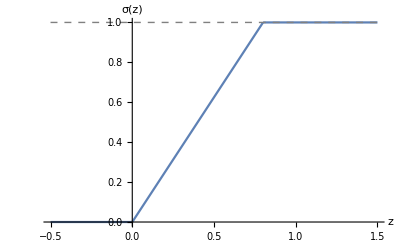

```mathematica
Plot[{σ[z,0.4,0.4],1},{z,-0.5,1.5},PlotRange->All,AxesLabel->{Style["z",FontSize->18],Style["σ(z)",FontSize->18]},
BaseStyle->{FontWeight->"Plain",FontSize->16},PlotStyle->{Default,{Thin,Gray,Dashed}}]
```